# 2D Tiling

## Used and explained in the article “On the K-theory of C^*-algebras for substitution tilings (a pedestrian version)” by Daniel Gonçalves and Maria Ramirez-Solano.

## 1.Definition of prototiles and substitution of prototiles (user input)

```mathematica
(*prototile = a polygon with a corner at the origin  = list of points in the plane, called locations, which represent the corners of the polygon, listed in counterclockwise order, starting at the origin*)
chairCorners={{0,0},{1,0},{2,0},{2,1},{1,1},{1,2},{0,2},{0,1}};
p1=chairCorners;
p2=Map[rotation90,p1];
p3=Map[rotation180,p1];
p4=Map[rotation270,p1];
prototiles={p1,p2,p3,p4};

(*inflation factor*)
λ=2;

(* tile = (prototilenumber, location) *)
(* tEdge = (tilenumber, edgenumber in the prototile) *)
(* tVertex = (tilenumber, vertexnumber in the prototile)  *)
(* protoEdge = (prototilenumber, edgenumber in the prototile) *)
(* protoVertex = (prototilenumber, vertexnumber in the prototile)  *)
(* wp0 = {(prototilenumber, location),(prototilenumber, location)... } = list of tiles*)
wp1={{1,{0,0}},{1,{1,1}},{2,{4,0}},{4,{0,4}}}; wp2={{2,rotation90[{0,0}]},{2,rotation90[{1,1}]},{3,rotation90[{4,0}]},{1,rotation90[{0,4}]}};
wp3={{3,rotation180[{0,0}]},{3,rotation180[{1,1}]},{4,rotation180[{4,0}]},{2,rotation180[{0,4}]}};
wp4={{4,rotation270[{0,0}]},{4,rotation270[{1,1}]},{1,rotation270[{4,0}]},{3,rotation270[{0,4}]}};
wPrototile={wp1,wp2,wp3,wp4};


MAXDegreeOfBoundaryVertices=1;(*USUALLY 1*)

(*auxiliary functions for constructing prototiles*)
rotation90=Function[location,{-location⟦2⟧,location⟦1⟧}];
rotation180=Function[location,-location];
rotation270=Function[location,{location⟦2⟧,-location⟦1⟧}];

color=Join[{Red,RGBColor[0,.71,.02],RGBColor[.15,.7,1],RGBColor[.8,.06,1],Green, Yellow, Orange,Blue,Cyan,Purple,LightBlue,LightGray,LightGreen,Red,Green, Yellow, Orange,Blue,Cyan,Purple,LightBlue,LightGray,LightGreen},Table[RGBColor[(i/8+.5)/1.5,0,0],{i,1,8}],
Table[RGBColor[0,(i/8+.5)/1.5,0],{i,1,8}],
Table[RGBColor[0,0,(i/4+.5)/1.5],{i,1,4}]]
label={a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z};
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

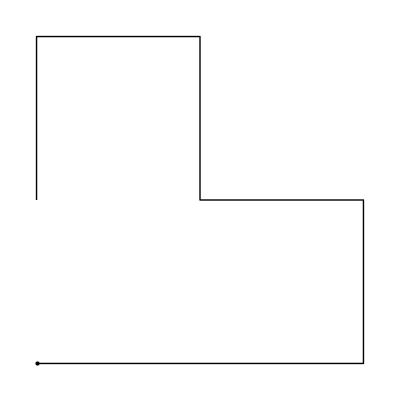
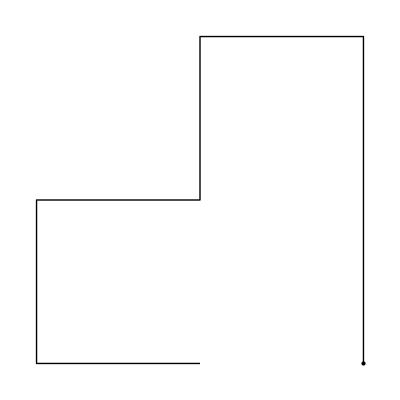
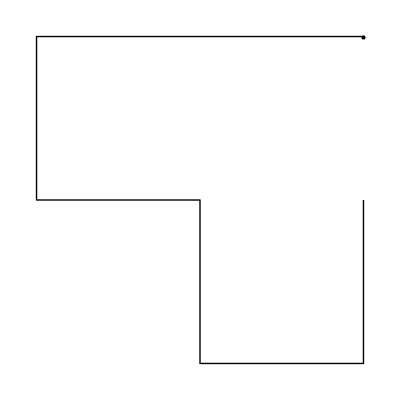
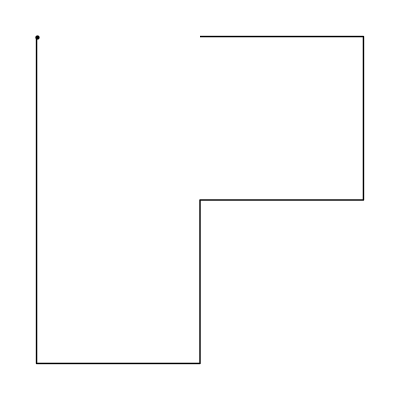

```mathematica
Map[Graphics[{Line[#],Point[#⟦1⟧]}]&,prototiles]
```

Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Thick],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

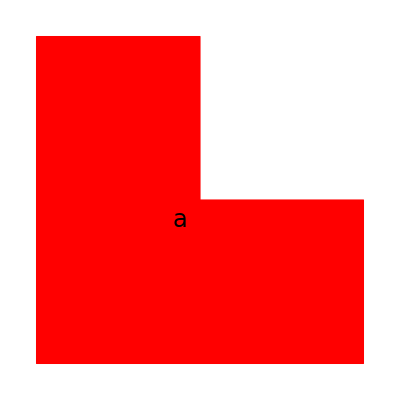
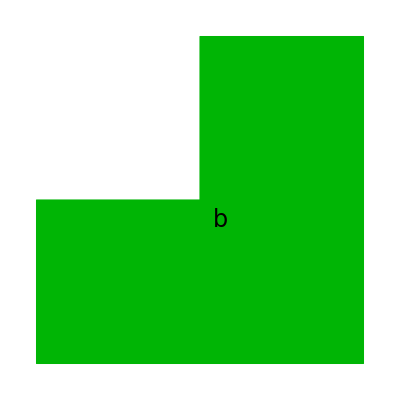
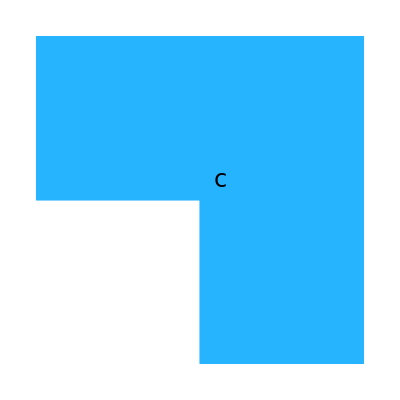
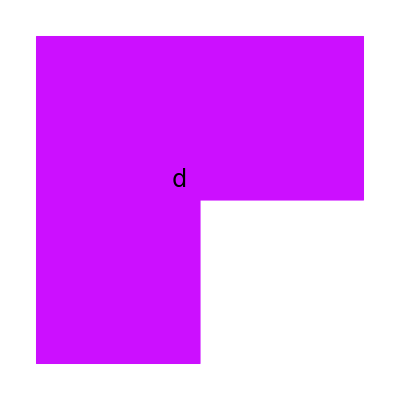

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]
polygonsLabels=Function[{polygonCorners,colorsIndices},Table[{
label⟦colorsIndices⟦i⟧⟧,Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]},
{i,1,Length[polygonCorners]}]];polygonsColorsBoundaries=Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Thick],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]

Table[Graphics[polygonsColorsBoundaries[{prototiles⟦i⟧},{i}]],{i,1,Length[prototiles]}]
```

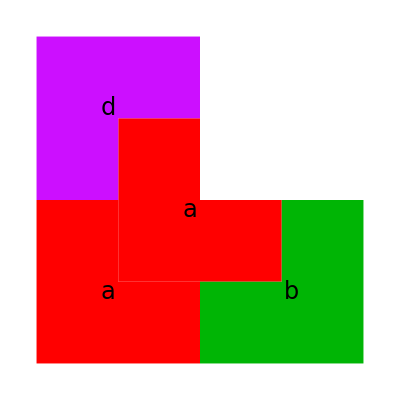
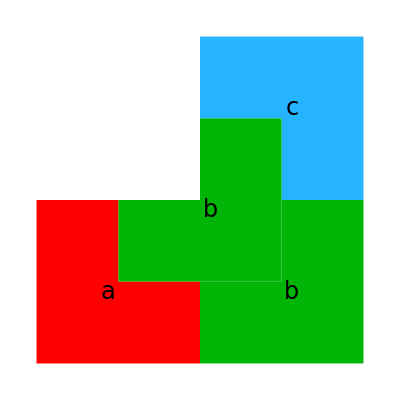
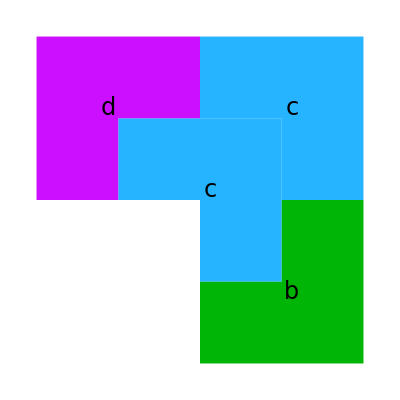
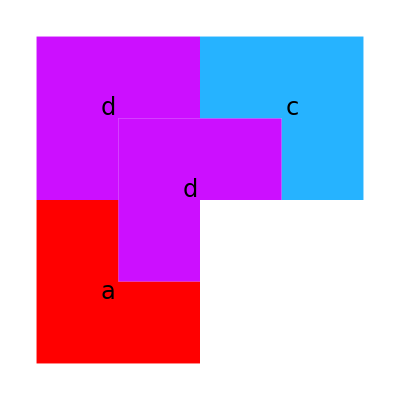

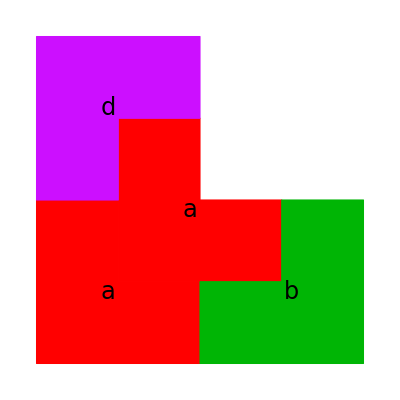
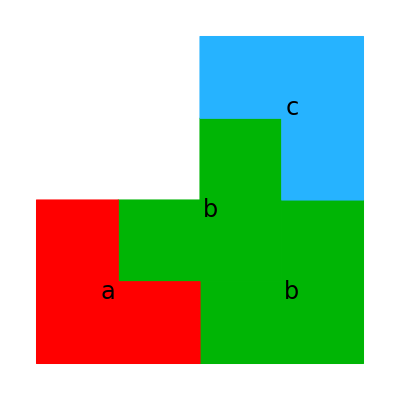
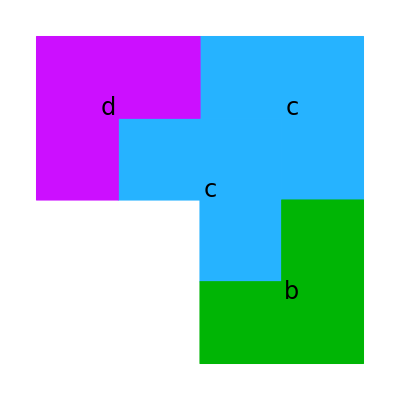
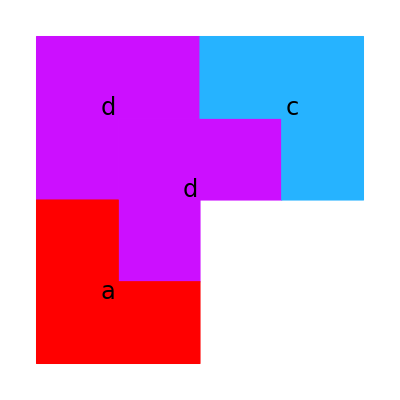

```mathematica
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];

Table[Graphics[polygonsColors[ComputeLocations[wPrototile⟦i⟧],Map[Transpose[#]⟦1⟧&,wPrototile]⟦i⟧]],{i,1,Length[wPrototile]}]
Table[Graphics[polygonsColorsBoundaries[ComputeLocations[wPrototile⟦i⟧],Map[Transpose[#]⟦1⟧&,wPrototile]⟦i⟧]],{i,1,Length[wPrototile]}]
```

## 2.Defining substitution ω(tiles) (run 1)

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColorsPlain=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Dashing[{0,Medium}]],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]


(*ωTile(tile) = list of tiles which represent the substituted tile  *)
ωTile=Function[tile,Module[{tiles,prototileNumber,translation},
{prototileNumber,translation}=tile;
tiles=wPrototile⟦prototileNumber⟧;
(*tiles +λ translation*)
Table[{tiles⟦i⟧⟦1⟧,tiles⟦i⟧⟦2⟧+ λ translation},{i,1,Length[tiles]}]
]];
(*AddTranslation=Function[{locations,translation},Table[locations⟦i⟧+translation,{i,1,Length[locations]}]];*)
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];
(*ω substitutes a list of tiles by substituting each tile individually *)
ω=Function[tiles,Flatten[Map[ωTile,tiles],1]]
supertile=Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

(*maximum number smaller than the limit*)
bsearchMin[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list⟦m⟧==elem,While[list⟦m⟧==elem,m++];
Return[m-1]];
If[list⟦m⟧<elem,n0=m+1,n1=m-1]];
If[list⟦m⟧<elem,m,m-1]];

(*minimum number larger than the limit*)
bsearchMax[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list[[m]]==elem,While[list[[m]]==elem,m--];
Return[m+1]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
If[list[[m]]>elem,m,m+1]];


varpepsilonZero=10^(-10);
positiveEdgeQ=Function[edgeLocation,Module[{x,y},{x,y}=edgeLocation⟦2⟧-edgeLocation⟦1⟧;If[x>0 || (Abs[x]<varpepsilonZero&&y>0),True,False]]];
(*computeEdgesDirections= {{1,1,1,-1,-1,,,},{1,1,-1,..}} where 1=samedirection, -1 opposite direction *)
computeEdgesDirections=Function[tileLocations,Module[{edge,lastedge},
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[positiveEdgeQ[edge]==True,1,-1],{i,1,Length[tileLocations]-1}],If[positiveEdgeQ[lastedge]==True,{1},{-1}]]]];
prototilesDirections=Map[computeEdgesDirections,prototiles]
prototilesLengths=Map[Length,prototiles]

Unflatten=Function[{list,lengths},Module[{k},
k=0;
Table[Table[k++;list⟦k⟧,{i,1,lengths⟦j⟧}],{j,1,Length[lengths]}]]];
swapVerticesofEdge=Function[v1v2,{v1v2⟦2⟧,v1v2⟦1⟧}];

cyclicRange=Function[{interval,n},Module[{a,b},
{a,b}=interval;
If[a≤ b,Range[a,b],
Join[Range[a,n],Range[b]]]]];
drawProtoEdge=Function[protoEdge,Module[{loc},
(*protoEdge={prototilenumber,number of edge on prototile} *)
loc=prototiles⟦protoEdge⟦1⟧⟧;
Graphics[{color⟦protoEdge⟦1⟧⟧,Polygon[loc], Black, Line[{loc⟦protoEdge⟦2⟧⟧,loc⟦Mod[protoEdge⟦2⟧+1,Length[loc],1]⟧}]}]]];
drawProtoVertex=Function[protoVertex,Module[{loc},loc=prototiles⟦protoVertex⟦1⟧⟧;Graphics[{color⟦protoVertex⟦1⟧⟧,Polygon[loc],Black,Point[{loc⟦protoVertex⟦2⟧⟧}]}]]];
```

Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Dashing[{0,Medium}]],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

Function[tiles,Flatten[ωTile/@tiles,1]]

Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

{{1,1,1,-1,1,-1,-1,-1},{1,1,-1,-1,-1,-1,1,1},{-1,-1,-1,1,-1,1,1,1},{-1,-1,1,1,1,1,-1,-1}}

{8,8,8,8}

```mathematica
(*ω(prototiles)*)
prototiles//Length
(*ω(prototiles)*)
prototiles//Length
Table[Graphics[polygonsColors[ComputeLocations[ωTile[{i,{0,0}}]],Map[#⟦1⟧&,ωTile[{i,{0,0}}]]]],{i,1,Length[prototiles]}]
```

4

4

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Expand[FullSimplify[supertile[1,3]]]
```

{{1,{0,0}},{1,{1,1}},{2,{4,0}},{4,{0,4}},{1,{2,2}},{1,{3,3}},{2,{6,2}},{4,{2,6}},{2,{8,0}},{2,{7,1}},{3,{8,4}},{1,{4,0}},{4,{0,8}},{4,{1,7}},{1,{0,4}},{3,{4,8}},{1,{4,4}},{1,{5,5}},{2,{8,4}},{4,{4,8}},{1,{6,6}},{1,{7,7}},{2,{10,6}},{4,{6,10}},{2,{12,4}},{2,{11,5}},{3,{12,8}},{1,{8,4}},{4,{4,12}},{4,{5,11}},{1,{4,8}},{3,{8,12}},{2,{16,0}},{2,{15,1}},{3,{16,4}},{1,{12,0}},{2,{14,2}},{2,{13,3}},{3,{14,6}},{1,{10,2}},{3,{16,8}},{3,{15,7}},{4,{12,8}},{2,{16,4}},{1,{8,0}},{1,{9,1}},{2,{12,0}},{4,{8,4}},{4,{0,16}},{4,{1,15}},{1,{0,12}},{3,{4,16}},{4,{2,14}},{4,{3,13}},{1,{2,10}},{3,{6,14}},{1,{0,8}},{1,{1,9}},{2,{4,8}},{4,{0,12}},{3,{8,16}},{3,{7,15}},{4,{4,16}},{2,{8,12}}}

```mathematica
Map[#[[1]]&,supertile[1,3]]
```

{1,1,2,4,1,1,2,4,2,2,3,1,4,4,1,3,1,1,2,4,1,1,2,4,2,2,3,1,4,4,1,3,2,2,3,1,2,2,3,1,3,3,4,2,1,1,2,4,4,4,1,3,4,4,1,3,1,1,2,4,3,3,4,2}

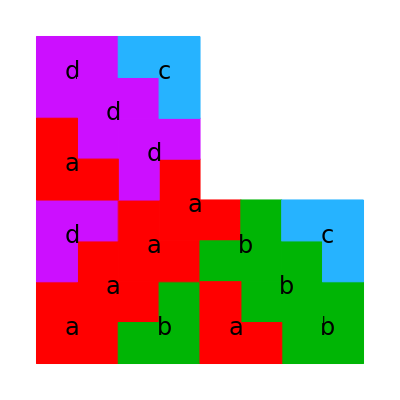

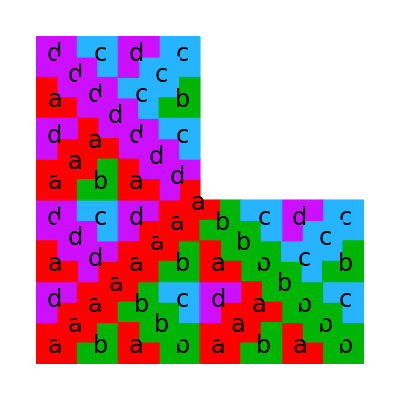

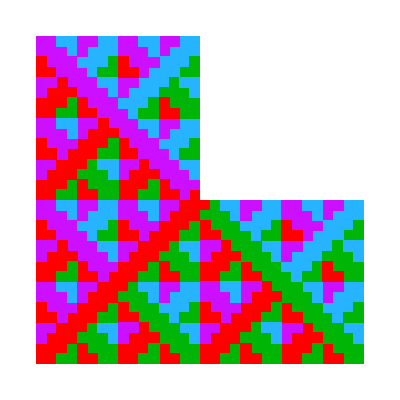

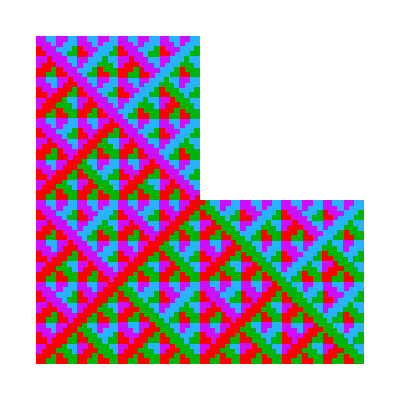

```mathematica
Graphics[polygonsColors[ComputeLocations[N[supertile[1,2]]],Map[#⟦1⟧&,supertile[1,2]]]]
Graphics[polygonsColors[ComputeLocations[N[supertile[1,3]]],Map[#⟦1⟧&,supertile[1,3]]]]
Graphics[polygonsColorsPlain[ComputeLocations[N[supertile[1,4]]],Map[#⟦1⟧&,supertile[1,4]]]]
Graphics[polygonsColorsPlain[ComputeLocations[N[supertile[1,5]]],Map[#⟦1⟧&,supertile[1,5]]]]
```

## 3.Computing Collared Tiles, stableEdges, collaredVertices (run 1,2)

```mathematica
timingList1={};
tiles=Expand[FullSimplify[supertile[1,5]]];
(*tilesLocations={tile1_written_as_list_of_locations, length of tile2_written_as_list_of_locations,...}. *)
AppendTo[timingList1,Timing[tilesLocations=ComputeLocations[tiles];"tilesLocations"]];
tilesLengths=Map[Length,tilesLocations];
(*tilesLocationsAsEdges={tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_of_positive_edges,...}. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
(*tilesEdgesDirections= directions of each tile where 1= same direction, -1=opposite directions. tile has counterclockwise direction. edge has positive direction.*)
(*AppendTo[timingList1,Timing[tilesEdgesDirections=Map[computeEdgesDirections,tilesLocations];"tilesEdgesDirections"]];*)
AppendTo[timingList1,Timing[tilesEdgesDirections=Map[prototilesDirections⟦#⟦1⟧⟧&,tiles];"tilesEdgesDirections"]];

computePositiveEdgesLocations=Function[{index},Module[{edge,lastedge,tileLocations},
tileLocations=tilesLocations⟦index⟧;
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[tilesEdgesDirections⟦index⟧⟦i⟧==1,edge,{edge⟦2⟧,edge⟦1⟧}],{i,1,Length[tileLocations]-1}],If[tilesEdgesDirections⟦index⟧⟦Length[tileLocations]⟧==1,{lastedge},{{lastedge⟦2⟧,lastedge⟦1⟧}}]]]];
AppendTo[timingList1,Timing[tilesLocationsAsEdges=Table[computePositiveEdgesLocations[i],{i,1,Length[tilesLocations]}];"tilesLocationsAsEdges"]];
(*accumulationsOfTilesLengths=Accumulate[{length of tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_positive_edges,... }]*)
accumulationsOfTilesLengths=Accumulate[tilesLengths];
(*tilesLocationsAsEdgesFlattened = list of all edges as pairs of locations (in the supertile)*)
tilesLocationsAsEdgesFlattened=Flatten[tilesLocationsAsEdges,1];
(*commonTilesLocationsAsEdgesIndices gives keysE and edgesToEdgesOfTiles (read below)*)
AppendTo[timingList1,Timing[positionIndexOftilesLocationsAsEdgesFlattened=Normal[PositionIndex[tilesLocationsAsEdgesFlattened]];"positionIndexOftilesLocationsAsEdgesFlattened"]];
(*edgesLocations = unique positive edges (i.e. the location of the positive edge is unique) *)
edgesLocations=Keys[positionIndexOftilesLocationsAsEdgesFlattened];
(*edgesToEdgesOfTiles = {{i1,i2},{i3,i4}...} where the positive edges at i1,i2, in tilesLocationsAsEdgesFlattened are the same.  *)
edgesToEdgesOfTiles=Values[positionIndexOftilesLocationsAsEdgesFlattened];
(*if {i1,i2} has length 2 then the edge at i1,i2 is an interior edge of the supertile. If it has length 1 then it is a bounded edge of the supertile:*)
{bEdges,iEdges}=Values[Sort[Normal[PositionIndex[Map[Length,edgesToEdgesOfTiles]]]]];
(*{bEdges,iEdges}=Values[PositionIndex[Map[Length,edgesToEdgesOfTiles]]];*)
iEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[iEdges]];
bEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[bEdges]];
iEdgesToSingletEdges=Map[#⟦1⟧&,iEdgesToEdgesOfTiles];
iEdgesLocations=tilesLocationsAsEdgesFlattened[[iEdgesToSingletEdges]];
bEdgesLocations=tilesLocationsAsEdgesFlattened[[Flatten[bEdgesToEdgesOfTiles]]];
(*  The tiling T contains the supertile; thus interior edges of the supertile are edges of the tiling T.
 An edge of the tiling T is a pair {(tile,indexOfEdgeInPrototile),(tile,indexOfEdgeInPrototile)}.
 edgeAsPairsOfPrototileNumbers =  {{prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}} Dictionary-sorted.
iEdgesAsPairsOfPrototileNumbers =  { Sort({prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}),...} !!This list has lots of multiplicities! *)
(*an interior edge in the supertile is a pair of edges that have common locations*)
bsearchMaxInaccumulationsOfTilesLengths[elem_]:=Module[{n0=1,n1=Length[accumulationsOfTilesLengths],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[accumulationsOfTilesLengths[[m]]==elem,While[accumulationsOfTilesLengths[[m]]==elem,m--];
Return[m+1]];
If[accumulationsOfTilesLengths[[m]]<elem,n0=m+1,n1=m-1]];
If[accumulationsOfTilesLengths[[m]]>elem,m,m+1]];

Clear[t1,i1,t2,i2]
unflattentedgeflattened=Function[tedgeflattenedNumber,Module[{tileNumber},
tileNumber=bsearchMaxInaccumulationsOfTilesLengths[tedgeflattenedNumber];
{tileNumber,If[tileNumber==1, tedgeflattenedNumber, tedgeflattenedNumber-accumulationsOfTilesLengths⟦tileNumber-1⟧]}]];
iEdgesAsPairsOfTiles=Map[Apply[Sort[{unflattentedgeflattened[#1],unflattentedgeflattened[#2]}]&,#]&,iEdgesToEdgesOfTiles];
iEdgesAsPairsOfPrototileNumbers=Table[{{t1,i1},{t2,i2}}=iEdgesAsPairsOfTiles⟦i⟧;Sort[{{tiles⟦t1⟧⟦1⟧,i1},{tiles⟦t2⟧⟦1⟧,i2}}],{i,1,Length[iEdgesAsPairsOfTiles]}];
Clear[t1,i1,t2,i2]
```

```mathematica
Take[tiles,10]//ColumnForm
tilesLocationsAsEdges//Length
```

{1,{0,0}}
{1,{1,1}}
{2,{4,0}}
{4,{0,4}}
{1,{2,2}}
{1,{3,3}}
{2,{6,2}}
{4,{2,6}}
{2,{8,0}}
{2,{7,1}}

1024

```mathematica
timingList1//ColumnForm
```

{0.01706,tilesLocations}
{0.00192,tilesEdgesDirections}
{0.04236,tilesLocationsAsEdges}
{0.01082,positionIndexOftilesLocationsAsEdgesFlattened}

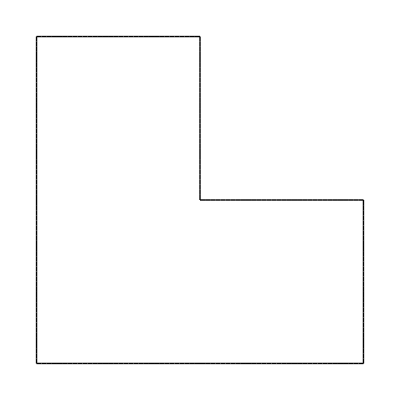

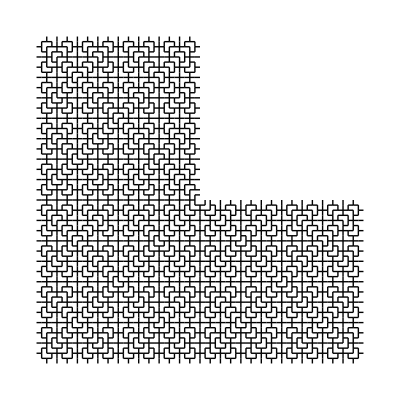

```mathematica
Graphics[Line[bEdgesLocations]]
Graphics[Line[iEdgesLocations]]
```

```mathematica
(*iEdgesAsPairsOfPrototileNumbers[[3]]
tilesLocationsAsEdges[[1]]
tilesLocationsAsEdges[[1]][[3]]
tilesLocationsAsEdges[[3]]
tilesLocationsAsEdges[[3]][[6]]*)
```

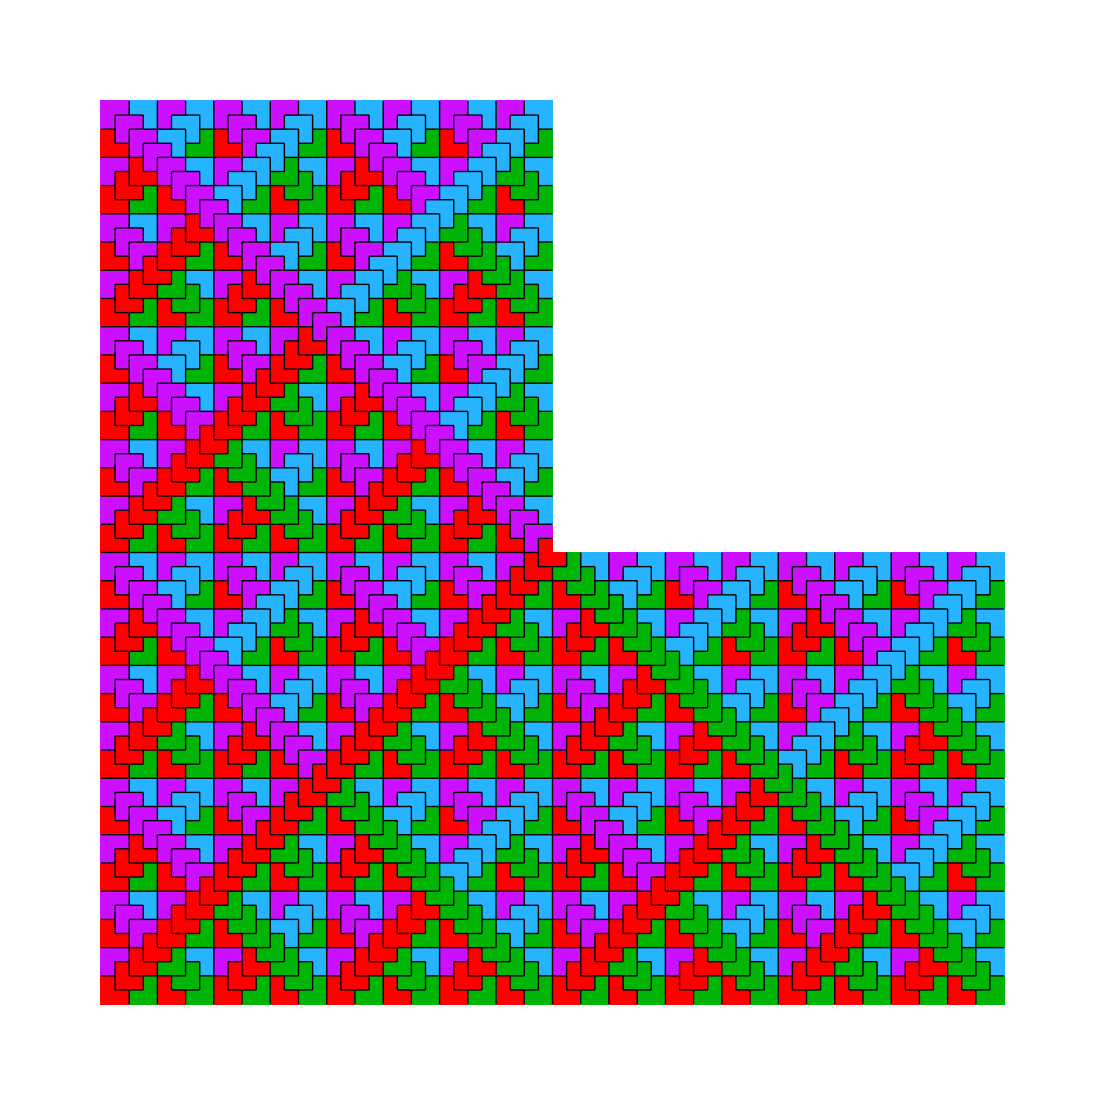

```mathematica
Show[Graphics[polygonsColorsPlain[ComputeLocations[supertile[1,5]],Map[#⟦1⟧&,supertile[1,5]]]],Graphics[Line[iEdgesLocations]]]
```

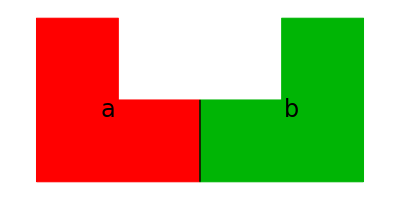

```mathematica
(*drawiEdges=Function[ieNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]}]];*)
drawiEdges=Function[ieNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Thick,Line[iEdgesLocations⟦ieNum⟧]}]];
drawiEdges[1]
```

```mathematica
iEdgesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[iEdgesAsPairsOfPrototileNumbers]]];
iEdgesRepresentatives//Length
sEdges=iEdgesAsPairsOfPrototileNumbers⟦iEdgesRepresentatives⟧
drawsEdges=Function[i,drawiEdges[iEdgesRepresentatives⟦i⟧]];
drawWsEdges=Function[seNum,Module[{se,wse},
se=Map[#⟦1⟧&,iEdgesAsPairsOfTiles⟦iEdgesRepresentatives⟦seNum⟧⟧];
wse=Flatten[Map[ωTile[tiles⟦#⟧]&,se],1];
Graphics[Join[polygonsColors[ComputeLocations[wse],Map[#⟦1⟧&,wse]],Map[Line,λ ComputeLocations[tiles⟦se⟧]]]]]];
```

44

{{{1,3},{2,6}},{{1,1},{1,4}},{{1,5},{1,8}},{{1,6},{4,3}},{{1,2},{2,5}},{{1,3},{2,4}},{{1,6},{4,5}},{{1,7},{4,4}},{{1,8},{2,1}},{{1,7},{2,2}},{{1,2},{2,3}},{{1,7},{4,6}},{{1,2},{4,7}},{{1,1},{4,8}},{{2,1},{2,4}},{{2,2},{3,3}},{{1,6},{2,7}},{{2,5},{2,8}},{{4,1},{4,4}},{{1,3},{4,2}},{{3,6},{4,7}},{{4,5},{4,8}},{{2,3},{3,6}},{{2,2},{3,5}},{{2,3},{3,4}},{{1,5},{2,6}},{{1,4},{2,7}},{{2,8},{3,1}},{{2,7},{3,2}},{{3,7},{4,2}},{{3,8},{4,1}},{{3,3},{4,6}},{{1,5},{4,2}},{{1,4},{4,3}},{{3,5},{4,6}},{{3,4},{4,7}},{{3,1},{3,4}},{{3,2},{4,3}},{{2,6},{3,7}},{{3,5},{3,8}},{{3,2},{4,5}},{{3,3},{4,4}},{{2,5},{3,6}},{{2,4},{3,7}}}

44

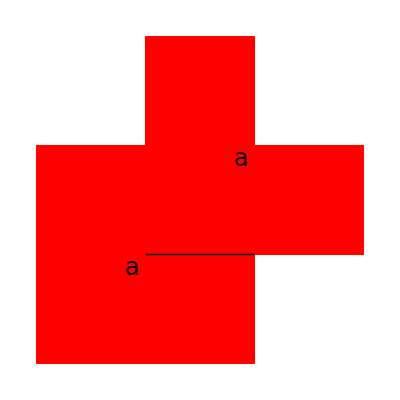
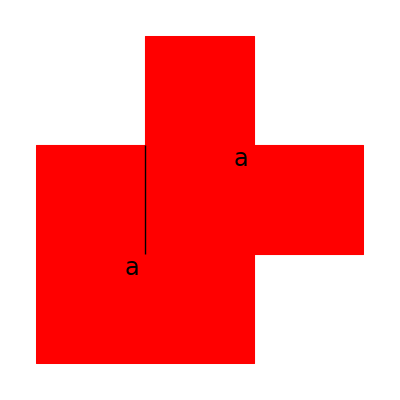
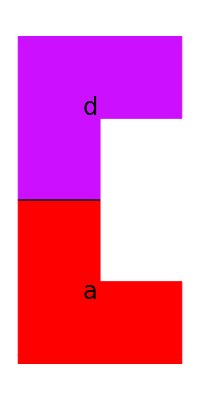
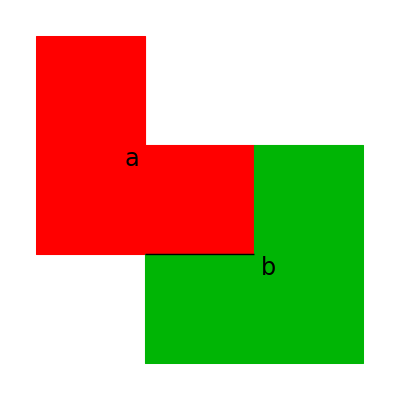
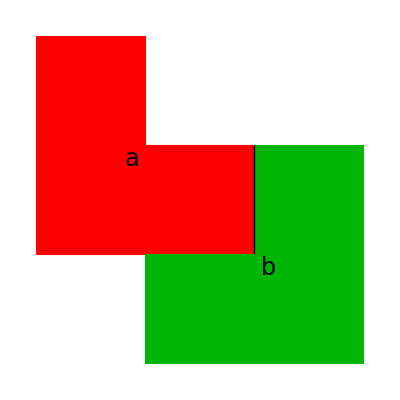
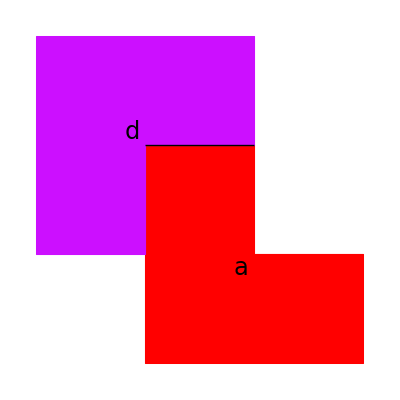
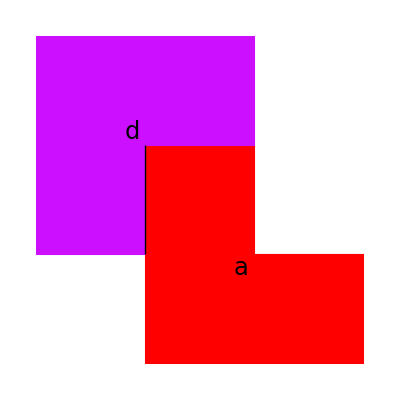
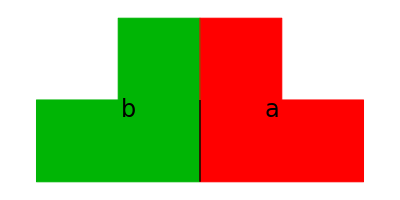
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*sEdges*)
iEdgesRepresentatives//Length
Map[drawiEdges,iEdgesRepresentatives]
```

```mathematica
xxx=Map[drawiEdges,iEdgesRepresentatives];
yyy=Table[Style[StringForm["se_(``)=",i],18],{i,1,Length[xxx]}];
Grid[Partition[Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,1,Length[xxx]}],5],Frame->All]
Grid[{Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,41,Length[xxx]}]},Frame->All]
```

se_1=
-Graphics- | se_2=
-Graphics- | se_3=
-Graphics- | se_4=
-Graphics- | se_5=
-Graphics-
se_6=
-Graphics- | se_7=
-Graphics- | se_8=
-Graphics- | se_9=
-Graphics- | se_10=
-Graphics-
se_11=
-Graphics- | se_12=
-Graphics- | se_13=
-Graphics- | se_14=
-Graphics- | se_15=
-Graphics-
se_16=
-Graphics- | se_17=
-Graphics- | se_18=
-Graphics- | se_19=
-Graphics- | se_20=
-Graphics-
se_21=
-Graphics- | se_22=
-Graphics- | se_23=
-Graphics- | se_24=
-Graphics- | se_25=
-Graphics-
se_26=
-Graphics- | se_27=
-Graphics- | se_28=
-Graphics- | se_29=
-Graphics- | se_30=
-Graphics-
se_31=
-Graphics- | se_32=
-Graphics- | se_33=
-Graphics- | se_34=
-Graphics- | se_35=
-Graphics-
se_36=
-Graphics- | se_37=
-Graphics- | se_38=
-Graphics- | se_39=
-Graphics- | se_40=
-Graphics-

se_41=
-Graphics- | se_42=
-Graphics- | se_43=
-Graphics- | se_44=
-Graphics-

```mathematica
(*iedgesLocationsAsVertices={positive_edge1, positive_edge2,...}, where these edges are interior edges of the supertile written as positive edges and their location is unique. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
iedgesLocationsAsVertices=iEdgesLocations;
(*iedgesLocationsAsVerticesFlattened = all possible vertices as locations (coming from the interior edges in the supertile)*)
iedgesLocationsAsVerticesFlattened=Flatten[iedgesLocationsAsVertices,1];
(*commonVerticesIndicesInEdgesLocationsAsVertices gives keysV and valuesV (read below)*)
positionIndexOfiedgesLocationsAsVerticesFlattened=PositionIndex[iedgesLocationsAsVerticesFlattened];
(*keysV = unique vertices (their location is unique) *)
verticesLocations=Keys[positionIndexOfiedgesLocationsAsVerticesFlattened];(*representatives of common locations of the vertices*)
(*valuesV = {{i1,i2...},{j3,j4...}...} where the vertices at i1,i2, in iedgesLocationsAsVerticesFlattened are the same. The goal is to obtain the edges with common vertices  *)
verticesToVerticesOfiEdges=Values[positionIndexOfiedgesLocationsAsVerticesFlattened];(* indices of keysV*)
(*if {i1,i2..} has length >1 then the vertex at i1,i2... is an interior vertex of the interior_edges of the supertile. 
If it has length 1 then it is a boundary vertex of the interior_edges of the supertile:*)

{boundaryVertices,interiorVertices}=Values[Sort[Normal[PositionIndex[Map[Length[#]>MAXDegreeOfBoundaryVertices&,verticesToVerticesOfiEdges]]]]];
interiorVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[interiorVertices]];
boundaryVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[boundaryVertices]];
interiorVerticesToSingleVerticesOfiEdges=Map[#⟦1⟧&,interiorVerticesToVerticesOfiEdges];
interiorVerticesLocations=iedgesLocationsAsVerticesFlattened[[interiorVerticesToSingleVerticesOfiEdges]];
boundaryVerticesLocations=iedgesLocationsAsVerticesFlattened[[Flatten[boundaryVerticesToVerticesOfiEdges]]];
tileNumberEdgeVertexTotileNumberVertex=Function[tileNumberEdgeVertex,Module[{tileNumber,edgeNumberOnTile,vertexNumberOnEdge,initialOrFinalVertexOnEdge,edgeDirection,vertexNumberOnTile},
{{tileNumber,edgeNumberOnTile},vertexNumberOnEdge}=tileNumberEdgeVertex;
edgeDirection=tilesEdgesDirections[[tileNumber]][[edgeNumberOnTile]];
vertexNumberOnTile=edgeNumberOnTile;
If[(edgeDirection==1 && vertexNumberOnEdge==2)||(edgeDirection==-1 && vertexNumberOnEdge==1),vertexNumberOnTile=Mod[vertexNumberOnTile+1,tilesLengths[[tileNumber]],1]];
{tileNumber,vertexNumberOnTile}]];

unflatteniEvertexflattened=Function[ievertexflattenedNumber,
{IntegerPart[(ievertexflattenedNumber+1)/2],Mod[ievertexflattenedNumber,2,1]}];
(*verticesAsListOfIndicesOfTiles={ (iEdgesAsPairsOfPrototileNumbers[positive_edge_i_index], 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
interiorVerticesAsiEdges=Table[Sort[Table[unflatteniEvertexflattened[interiorVerticesToVerticesOfiEdges⟦j⟧⟦i⟧],{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

(*protoVerticesAsListOfIndicesOfEdges={ (positive_edge_i_index, 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
verticesAsListOfTilesEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfTiles⟦iEdgeNumber⟧,index},{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

verticesAsListOfTilesVNumbers=Table[Union[Flatten[Table[{{e1,e2},v}=verticesAsListOfTilesEVNumbers[[j]][[i]];
{tileNumberEdgeVertexTotileNumberVertex[{e1,v}],
tileNumberEdgeVertexTotileNumberVertex[{e2,v}]},{i,1,Length[verticesAsListOfTilesEVNumbers[[j]]]}],1]],{j,1,Length[verticesAsListOfTilesEVNumbers]}];

verticesAsListOfPrototileEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfPrototileNumbers⟦iEdgeNumber⟧,index},
{i,1,Length[interiorVerticesAsiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesAsiEdges]}];

verticesAsListOfPrototileVNumbers=Table[Sort[Table[
{tileNumber,index}=verticesAsListOfTilesVNumbers⟦j⟧⟦i⟧;
{tiles⟦tileNumber⟧⟦1⟧,index},
{i,1,Length[verticesAsListOfTilesVNumbers⟦j⟧]}]],{j,1,Length[verticesAsListOfTilesVNumbers]}];
```

```mathematica
verticesAsListOfPrototileVNumbers//Tally//Length
Take[verticesAsListOfPrototileVNumbers//Tally,10]//ColumnForm
```

47

{{{1,2},{1,4},{2,6}},72}
{{{1,1},{1,5}},143}
{{{1,6},{1,8},{4,4}},72}
{{{1,3},{2,5}},72}
{{{1,2},{1,4},{2,4}},71}
{{{1,6},{1,8},{4,6}},71}
{{{1,7},{4,5}},72}
{{{1,8},{2,2}},113}
{{{1,3},{1,7},{2,3},{2,7}},36}
{{{1,3},{1,7},{4,3},{4,7}},36}

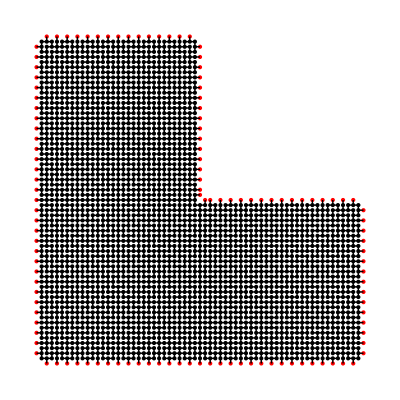

```mathematica
(*boundary vertices should be shown in RED. Interior vertices in Black *)
Show[Graphics[{Red,Point[boundaryVerticesLocations]}],
Graphics[Point[interiorVerticesLocations]],Graphics[Line[iEdgesLocations]]]
```

```mathematica
iEdgesToEdgesOfTiles[[{1,2,5}]]==edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,iEdgesToEdgesOfTiles[[{1,2,5}]]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]]]]
```

True

True

True

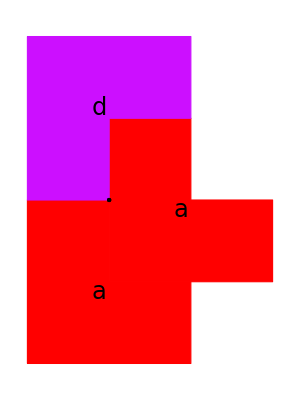

```mathematica
(*drawInteriorVertex=Function[ivNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];*)
drawInteriorVertex=Function[ivNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];
drawInteriorVertex[3]
```

```mathematica
(*drawVertex=Function[index,{drawVertexWithTileLocations[index],drawVertexWithEdges[index]}];
drawVertexWithEdges=Function[index,Line[iedgesLocationsAsVertices⟦Map[#⟦1⟧&,interiorVerticesAsiEdges⟦index⟧]⟧]];
drawVertexWithTileLocations=Function[index,Module[{vertexAsListOfIndicesOfEdges,vertexAsListOfIndicesOfTiles},
vertexAsListOfIndicesOfEdges=Map[#⟦1⟧&,interiorVerticesAsiEdges⟦index⟧];
vertexAsListOfIndicesOfTiles=Union[Flatten[Map[{#⟦1⟧⟦1⟧,#⟦2⟧⟦1⟧}&,iEdgesAsPairsOfTiles⟦vertexAsListOfIndicesOfEdges⟧]]];
PolygonsInColor[tilesLocations⟦vertexAsListOfIndicesOfTiles⟧]]];
PolygonsInColor=Function[polygonCornersList, Table[{color⟦Mod[i,Length[polygonCornersList],1]⟧,Polygon[polygonCornersList⟦i⟧]},{i,1,Length[polygonCornersList]}]];
*)
```

```mathematica
(*drawProtoVertex=Function[protoVertex, Module[{prototileNumber1,prototileNumber2,edgeIndex1,edgeIndex2,vertexIndex,e1,e2,v1,v2},
Table[{{{prototileNumber1,edgeIndex1},{prototileNumber2,edgeIndex2}},vertexIndex}=protoVertex⟦i⟧;
e1=grabEdgeInPolygon[prototiles⟦prototileNumber1⟧,edgeIndex1];
v1=grabVertexInEdgeInPolygon[e1,vertexIndex];
e2=grabEdgeInPolygon[prototiles⟦prototileNumber2⟧,edgeIndex2];
v2=grabVertexInEdgeInPolygon[e2,vertexIndex];

{ {{color⟦Mod[i,Length[color],1]⟧,Polygon[prototiles⟦prototileNumber1⟧]},
{Blue,Line[e1]},{Black,PointSize[.05],Point[v1]}},
{{color⟦Mod[i,Length[color],1]⟧,Polygon[prototiles⟦prototileNumber2⟧]},{Blue,Line[e2]},{Black,PointSize[.05],Point[v2]}}},{i,1,Length[protoVertex]}]
]];

grabEdgeInPolygon=Function[{polygonCorners,edge},{polygonCorners⟦edge⟧,polygonCorners⟦Mod[edge+1,Length[polygonCorners],1]⟧}];
grabVertexInEdgeInPolygon=Function[{edgeAsLocations,initialOrFinalVertex}, If[positiveEdgeQ[edgeAsLocations]==True,edgeAsLocations⟦initialOrFinalVertex⟧,edgeAsLocations⟦Mod[initialOrFinalVertex+1,2,1]⟧]];
Map[Graphics,Flatten[drawProtoVertex[verticesAsListOfPrototileEVNumbers[[1]]],1]]
*)
```

```mathematica
iVerticesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[verticesAsListOfPrototileVNumbers]]];
iVerticesRepresentatives//Length
cVertices=verticesAsListOfPrototileVNumbers⟦iVerticesRepresentatives⟧
drawcVertices=Function[index,drawInteriorVertex[iVerticesRepresentatives⟦index⟧]];
drawWcVertices=Function[cvNum,Module[{cv,wcv},
cv=Map[#⟦1⟧&,verticesAsListOfTilesVNumbers⟦iVerticesRepresentatives⟦cvNum⟧⟧];
wcv=Flatten[Map[ωTile[tiles⟦#⟧]&,cv],1];
Graphics[Join[polygonsColors[ComputeLocations[wcv],Map[#⟦1⟧&,wcv]],Map[Line,λ ComputeLocations[tiles⟦cv⟧]]]]]];
```

47

{{{1,2},{1,4},{2,6}},{{1,1},{1,5}},{{1,6},{1,8},{4,4}},{{1,3},{2,5}},{{1,2},{1,4},{2,4}},{{1,6},{1,8},{4,6}},{{1,7},{4,5}},{{1,8},{2,2}},{{1,3},{1,7},{2,3},{2,7}},{{1,3},{1,7},{4,3},{4,7}},{{1,2},{4,8}},{{2,1},{2,5}},{{2,2},{2,4},{3,4}},{{1,3},{2,3},{2,7},{3,3}},{{1,6},{2,6},{2,8}},{{1,4},{4,2},{4,4}},{{4,1},{4,5}},{{1,7},{3,7},{4,3},{4,7}},{{3,6},{4,6},{4,8}},{{1,7},{2,3},{3,7},{4,3}},{{2,2},{2,4},{3,6}},{{1,4},{2,6},{2,8}},{{2,3},{3,5}},{{1,5},{2,7}},{{2,8},{3,2}},{{1,1},{2,1},{3,1},{4,1}},{{3,8},{4,2}},{{1,6},{4,2},{4,4}},{{3,4},{4,6},{4,8}},{{1,3},{2,7},{3,3},{4,7}},{{1,5},{4,3}},{{3,5},{4,7}},{{2,3},{3,3},{3,7},{4,3}},{{1,3},{1,7},{2,7},{4,7}},{{1,3},{1,7},{2,3},{4,3}},{{2,7},{3,3},{3,7},{4,7}},{{2,3},{2,7},{3,3},{3,7}},{{3,2},{3,4},{4,4}},{{3,1},{3,5}},{{2,6},{3,6},{3,8}},{{3,2},{3,4},{4,6}},{{2,4},{3,6},{3,8}},{{3,3},{4,5}},{{2,5},{3,7}},{{3,3},{3,7},{4,3},{4,7}},{{1,3},{3,3},{4,3},{4,7}},{{1,7},{2,3},{2,7},{3,7}}}

47

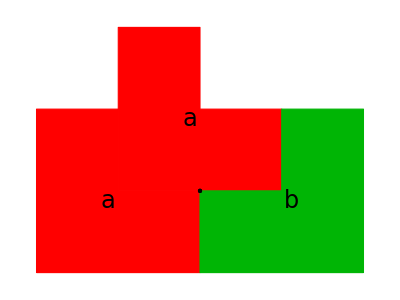
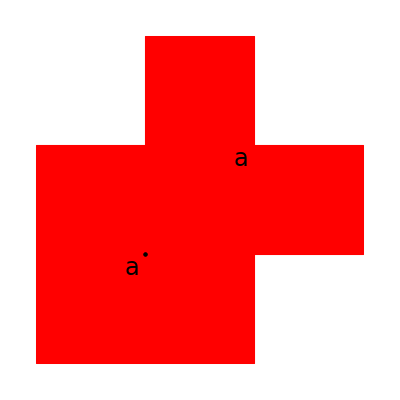
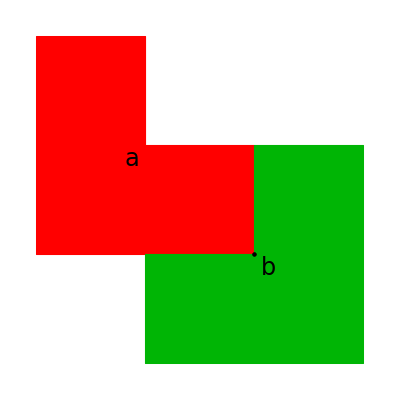
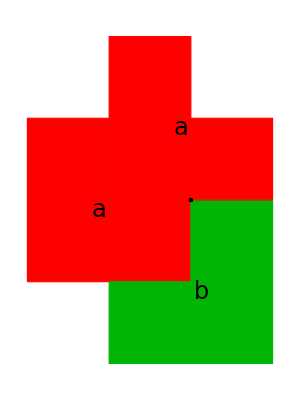
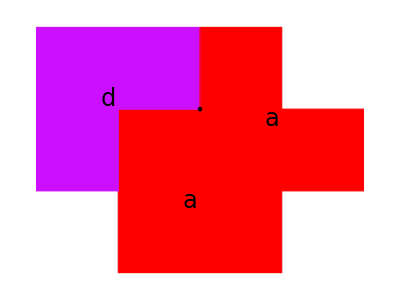
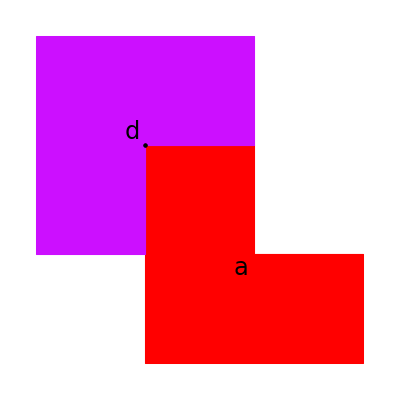
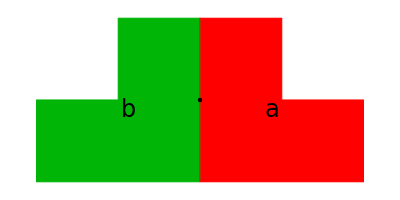
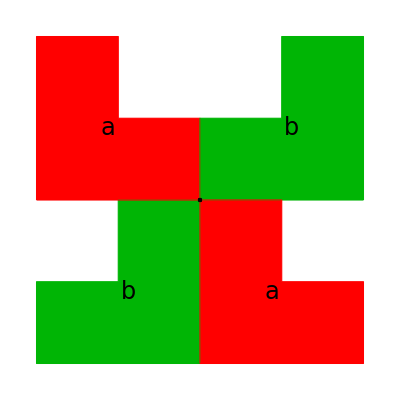
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* protovertices == collared vertices *)
iVerticesRepresentatives//Length
Map[drawInteriorVertex,iVerticesRepresentatives]
```

```mathematica
xxx=Map[drawInteriorVertex,iVerticesRepresentatives];
yyy=Table[Style[StringForm["sv_(``)=",i],18],{i,1,Length[xxx]}];
Grid[Partition[Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,1,Length[xxx]}],5],Frame->All]
Grid[{Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,46,Length[xxx]}]},Frame->All]
```

sv_1=
-Graphics- | sv_2=
-Graphics- | sv_3=
-Graphics- | sv_4=
-Graphics- | sv_5=
-Graphics-
sv_6=
-Graphics- | sv_7=
-Graphics- | sv_8=
-Graphics- | sv_9=
-Graphics- | sv_10=
-Graphics-
sv_11=
-Graphics- | sv_12=
-Graphics- | sv_13=
-Graphics- | sv_14=
-Graphics- | sv_15=
-Graphics-
sv_16=
-Graphics- | sv_17=
-Graphics- | sv_18=
-Graphics- | sv_19=
-Graphics- | sv_20=
-Graphics-
sv_21=
-Graphics- | sv_22=
-Graphics- | sv_23=
-Graphics- | sv_24=
-Graphics- | sv_25=
-Graphics-
sv_26=
-Graphics- | sv_27=
-Graphics- | sv_28=
-Graphics- | sv_29=
-Graphics- | sv_30=
-Graphics-
sv_31=
-Graphics- | sv_32=
-Graphics- | sv_33=
-Graphics- | sv_34=
-Graphics- | sv_35=
-Graphics-
sv_36=
-Graphics- | sv_37=
-Graphics- | sv_38=
-Graphics- | sv_39=
-Graphics- | sv_40=
-Graphics-
sv_41=
-Graphics- | sv_42=
-Graphics- | sv_43=
-Graphics- | sv_44=
-Graphics- | sv_45=
-Graphics-

sv_46=
-Graphics- | sv_47=
-Graphics-

### results

```mathematica
sEdges
```

{{{1,3},{2,6}},{{1,1},{1,4}},{{1,5},{1,8}},{{1,6},{4,3}},{{1,2},{2,5}},{{1,3},{2,4}},{{1,6},{4,5}},{{1,7},{4,4}},{{1,8},{2,1}},{{1,7},{2,2}},{{1,2},{2,3}},{{1,7},{4,6}},{{1,2},{4,7}},{{1,1},{4,8}},{{2,1},{2,4}},{{2,2},{3,3}},{{1,6},{2,7}},{{2,5},{2,8}},{{4,1},{4,4}},{{1,3},{4,2}},{{3,6},{4,7}},{{4,5},{4,8}},{{2,3},{3,6}},{{2,2},{3,5}},{{2,3},{3,4}},{{1,5},{2,6}},{{1,4},{2,7}},{{2,8},{3,1}},{{2,7},{3,2}},{{3,7},{4,2}},{{3,8},{4,1}},{{3,3},{4,6}},{{1,5},{4,2}},{{1,4},{4,3}},{{3,5},{4,6}},{{3,4},{4,7}},{{3,1},{3,4}},{{3,2},{4,3}},{{2,6},{3,7}},{{3,5},{3,8}},{{3,2},{4,5}},{{3,3},{4,4}},{{2,5},{3,6}},{{2,4},{3,7}}}

```mathematica
cVertices
```

{{{1,2},{1,4},{2,6}},{{1,1},{1,5}},{{1,6},{1,8},{4,4}},{{1,3},{2,5}},{{1,2},{1,4},{2,4}},{{1,6},{1,8},{4,6}},{{1,7},{4,5}},{{1,8},{2,2}},{{1,3},{1,7},{2,3},{2,7}},{{1,3},{1,7},{4,3},{4,7}},{{1,2},{4,8}},{{2,1},{2,5}},{{2,2},{2,4},{3,4}},{{1,3},{2,3},{2,7},{3,3}},{{1,6},{2,6},{2,8}},{{1,4},{4,2},{4,4}},{{4,1},{4,5}},{{1,7},{3,7},{4,3},{4,7}},{{3,6},{4,6},{4,8}},{{1,7},{2,3},{3,7},{4,3}},{{2,2},{2,4},{3,6}},{{1,4},{2,6},{2,8}},{{2,3},{3,5}},{{1,5},{2,7}},{{2,8},{3,2}},{{1,1},{2,1},{3,1},{4,1}},{{3,8},{4,2}},{{1,6},{4,2},{4,4}},{{3,4},{4,6},{4,8}},{{1,3},{2,7},{3,3},{4,7}},{{1,5},{4,3}},{{3,5},{4,7}},{{2,3},{3,3},{3,7},{4,3}},{{1,3},{1,7},{2,7},{4,7}},{{1,3},{1,7},{2,3},{4,3}},{{2,7},{3,3},{3,7},{4,7}},{{2,3},{2,7},{3,3},{3,7}},{{3,2},{3,4},{4,4}},{{3,1},{3,5}},{{2,6},{3,6},{3,8}},{{3,2},{3,4},{4,6}},{{2,4},{3,6},{3,8}},{{3,3},{4,5}},{{2,5},{3,7}},{{3,3},{3,7},{4,3},{4,7}},{{1,3},{3,3},{4,3},{4,7}},{{1,7},{2,3},{2,7},{3,7}}}

## 4. Exponential Matrix, Index Matrix (run 1,2,3)

```mathematica
(*exponential matrix*)
cVerticesAssEdges=verticesAsListOfPrototileEVNumbers[[iVerticesRepresentatives]];
sEdgescVerticesMatrix=ConstantArray[0,{Length[sEdges],Length[cVertices]}];

sEdgescVerticesMatrixIndicesFunction=
Function[cvNumber,Module[{cv,se,vInitialOrFinal,seNumber,value},
cv=cVerticesAssEdges⟦cvNumber⟧;
Table[{se,vInitialOrFinal}=cv⟦i⟧;
seNumber=Position[sEdges,se]⟦1⟧⟦1⟧;
value=If[vInitialOrFinal==1,-1,1];
sEdgescVerticesMatrix⟦seNumber⟧⟦cvNumber⟧+=value;
{{seNumber,cvNumber},value},{i,1,Length[cv]}]]];


sEdgescVerticesMatrixIndices=Table[sEdgescVerticesMatrixIndicesFunction[i],{i,1,Length[cVertices]}];
(*stableEdges-collardVertices Matrix (se1=-cv1+cv9+cv14...*)
Print["δ^0=",sEdgescVerticesMatrix//MatrixForm]
```

δ^0=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0)

```mathematica
(*Index Matrix*)
prototilessEdgesMatrix=ConstantArray[0,{Length[prototiles],Length[sEdges]}];
Table[{{p1,e1},{p2,e2}}=sEdges⟦sedgeNumber⟧;
prototilessEdgesMatrix⟦p1⟧⟦sedgeNumber⟧+=prototilesDirections⟦p1⟧⟦e1⟧;
prototilessEdgesMatrix⟦p2⟧⟦sedgeNumber⟧+=prototilesDirections⟦p2⟧⟦e2⟧;,
{sedgeNumber,1,Length[sEdges]}];
Print["δ^1=",prototilessEdgesMatrix//MatrixForm]
```

δ^1=(1 | 0 | 0 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | -1 | 1 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 1 | 0 | 0 | -1 | -1 | 1 | 1 | -1 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | -1 | -1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0)

```mathematica
prototilessEdgesMatrix.sEdgescVerticesMatrix//Max
prototilessEdgesMatrix.sEdgescVerticesMatrix//Min
```

0

0

## 5. Homotopy matrices Wv, We, Wf

```mathematica
(*Homotopy ω(prototile) --> prototile : Hverticesp1t1 is the image of the map on the vertices from ω(prototile) to same protitile 1.*)
Hverticesp1t1={1,2,2,2,1,8,8,8};
Hverticesp1t2={1,2,3,4,5,6,7,8};
Hverticesp1t3={3,4,4,4,3,2,2,2};
Hverticesp1t4={7,8,8,8,7,6,6,6};

Hverticesp1={2,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp2={2,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp3={2,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp4={2,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hvertices={Hverticesp1,Hverticesp2,Hverticesp3,Hverticesp4}
```

{{2,{{1,2,2,2,1,8,8,8},{1,2,3,4,5,6,7,8},{3,4,4,4,3,2,2,2},{7,8,8,8,7,6,6,6}}},{2,{{1,2,2,2,1,8,8,8},{1,2,3,4,5,6,7,8},{3,4,4,4,3,2,2,2},{7,8,8,8,7,6,6,6}}},{2,{{1,2,2,2,1,8,8,8},{1,2,3,4,5,6,7,8},{3,4,4,4,3,2,2,2},{7,8,8,8,7,6,6,6}}},{2,{{1,2,2,2,1,8,8,8},{1,2,3,4,5,6,7,8},{3,4,4,4,3,2,2,2},{7,8,8,8,7,6,6,6}}}}

```mathematica
wPrototileNumbers=Table[Map[#⟦1⟧&,wPrototile⟦i⟧],{i,1,Length[wPrototile]}]

drawHomotopyVerticesOfTilesNoGraphics=Function[tile,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
{t,imageVertices}=Hvertices⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopycVertices=Function[cVertexNum,Module[{cv},
cv=cVertices⟦cVertexNum⟧;
Graphics[Map[drawHomotopyVerticesOfTilesNoGraphics,Table[{cv⟦i,1⟧,Expand[FullSimplify[prototiles⟦cv⟦i,1⟧,1⟧-prototiles⟦cv⟦i,1⟧,cv⟦i,2⟧⟧]]},{i,1,Length[cv]}]]]]];

drawHomotopyVerticesOfTiles=Function[tile,Module[{locs,t,imageloc,arrows},
locs=ComputeLocations[ωTile[tile]];
{t,imageVertices}=Hvertices⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]]];

drawHomotopyVertices=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
{t,imageVertices}=Hvertices⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,Flatten[wPrototile,1]]],arrows}]
]];

drawHomotopyVerticesAll=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
{t,imageVertices}=Hvertices⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,Flatten[wPrototile,1]]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,Flatten[wPrototile,1]]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

{{1,1,2,4},{2,2,3,1},{3,3,4,2},{4,4,1,3}}

```mathematica
Table[drawHomotopyVerticesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[drawHomotopyVertices[i],{i,1,Length[prototiles]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawHomotopycVertices[1]
```

-Graphics-

```mathematica
(*Drawing the homotopy on the vertices*)
```

```mathematica
drawHomotopyVertices[1][[1]]
```

{{{EdgeForm[Dashing[{0,Medium}]],-Graphics-,Polygon[{{0,0},{1,0},{2,0},{2,1},{1,1},{1,2},{0,2},{0,1}}],Text[a,{7/8,7/8}]},{EdgeForm[Dashing[{0,Medium}]],-Graphics-,Polygon[{{1,1},{2,1},{3,1},{3,2},{2,2},{2,3},{1,3},{1,2}}],Text[a,{15/8,15/8}]},{EdgeForm[Dashing[{0,Medium}]],-Graphics-,Polygon[{{4,0},{4,1},{4,2},{3,2},{3,1},{2,1},{2,0},{3,0}}],Text[b,{25/8,7/8}]},{EdgeForm[Dashing[{0,Medium}]],-Graphics-,Polygon[{{0,4},{0,3},{0,2},{1,2},{1,3},{2,3},{2,4},{1,4}}],Text[d,{7/8,25/8}]}},{Arrow[{{{0,0},{0,0}},{{1,0},{2,0}},{{2,0},{2,0}},{{2,1},{2,0}},{{1,1},{0,0}},{{1,2},{0,2}},{{0,2},{0,2}},{{0,1},{0,2}}}],Arrow[{{{1,1},{0,0}},{{2,1},{2,0}},{{3,1},{4,0}},{{3,2},{4,2}},{{2,2},{2,2}},{{2,3},{2,4}},{{1,3},{0,4}},{{1,2},{0,2}}}],Arrow[{{{4,0},{4,0}},{{4,1},{4,2}},{{4,2},{4,2}},{{3,2},{4,2}},{{3,1},{4,0}},{{2,1},{2,0}},{{2,0},{2,0}},{{3,0},{2,0}}}],Arrow[{{{0,4},{0,4}},{{0,3},{0,2}},{{0,2},{0,2}},{{1,2},{0,2}},{{1,3},{0,4}},{{2,3},{2,4}},{{2,4},{2,4}},{{1,4},{2,4}}}]}}

```mathematica
{{{EdgeForm[{Dashing[{0,Small}],Black}],White,Polygon[{{0,0},{1,0},{2,0},{2,1},{1,1},{1,2},{0,2},{0,1}}],Text[,{7/8,7/8}]},{EdgeForm[{Dashing[{0,Small}],Black}],White,Polygon[{{1,1},{2,1},{3,1},{3,2},{2,2},{2,3},{1,3},{1,2}}],Text[,{15/8,15/8}]},{EdgeForm[{Dashing[{0,Small}],Black}],White,Polygon[{{4,0},{4,1},{4,2},{3,2},{3,1},{2,1},{2,0},{3,0}}],Text[,{25/8,7/8}]},{EdgeForm[{Dashing[{0,Small}],Black}],White,Polygon[{{0,4},{0,3},{0,2},{1,2},{1,3},{2,3},{2,4},{1,4}}],Text[,{7/8,25/8}]}},
{
PointSize[Medium],Point[{{0,0},{1,0},{2,0},{2,1},{1,1},{1,2},{0,2},{0,1}}],
PointSize[Medium],Point[{{1,1},{2,1},{3,1},{3,2},{2,2},{2,3},{1,3},{1,2}}],
PointSize[Medium],Point[{{4,0},{4,1},{4,2},{3,2},{3,1},{2,1},{2,0},{3,0}}],
PointSize[Medium],Point[{{0,4},{0,3},{0,2},{1,2},{1,3},{2,3},{2,4},{1,4}}],
Text[Style[Subscript[h, s],FontFamily->"Times New Roman",18],{.7,.5}]
},,{Thick,Arrow[{{{0,0},{0,0}},{{1,0},{2,0}},{{2,0},{2,0}},{{2,1},{2,0}},{{1,1},{0,0}},{{1,2},{0,2}},{{0,2},{0,2}},{{0,1},{0,2}}}],Arrow[{{{1,1},{0,0}},{{2,1},{2,0}},{{3,1},{4,0}},{{3,2},{4,2}},{{2,2},{2,2}},{{2,3},{2,4}},{{1,3},{0,4}},{{1,2},{0,2}}}],Arrow[{{{4,0},{4,0}},{{4,1},{4,2}},{{4,2},{4,2}},{{3,2},{4,2}},{{3,1},{4,0}},{{2,1},{2,0}},{{2,0},{2,0}},{{3,0},{2,0}}}],Arrow[{{{0,4},{0,4}},{{0,3},{0,2}},{{0,2},{0,2}},{{1,2},{0,2}},{{1,3},{0,4}},{{2,3},{2,4}},{{2,4},{2,4}},{{1,4},{2,4}}}]}}//Graphics
```

-Graphics-

```mathematica
i=1
```

1

```mathematica
homotopycVertices=ConstantArray[0,Length[cVertices]];

Clear[cv,ps,vs,locsH,xx,yy,ts,cvNum]
For[cvNum=1,cvNum≤ Length[cVertices],cvNum++,
cv=cVertices⟦cvNum⟧;
cvHpreimage=Table[Position[Hvertices⟦cv⟦i,1⟧,2⟧,cv⟦i,2⟧],{i,1,Length[cv]}];
{ps,vs}=Transpose[cv];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototiles⟦ps⟦i⟧⟧⟦vs⟦i⟧⟧},{i,1,Length[ps]}];
(*Map[ωTile,ts]*)
locsH=Table[ComputeLocations[ωTile[ts⟦i⟧]],{i,1,Length[ts]}];
cvHpreimageLocations=Table[Table[locsH⟦j⟧⟦cvHpreimage⟦j⟧⟦i,1⟧,cvHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[cvHpreimage⟦j⟧]}],{j,1,Length[cvHpreimage]}];
(*cvHpreimage//ColumnForm*)
(*cvHpreimageLocations//Point//Graphics*)
(*Flatten[cvHpreimageLocations,1]*)
cvHpreimageFlattened=Flatten[cvHpreimage,1];
(*cvHpreimageFlattenedTiles=Flatten[Table[ConstantArray[i,Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1]*)
cvHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1];
hcverticesindices=Values[Normal[PositionIndex[Flatten[cvHpreimageLocations,1]]]];

(*hcverticesAsTiles=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedTiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[Flatten[{yy⟦i⟧,xx⟦i⟧}],{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}]
Table[Map[locsH⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧&,hcverticesAsTiles⟦i⟧],{i,1,Length[hcverticesAsTiles]}]*)

hcvertices=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedPrototiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}];
homotopycVertices⟦cvNum⟧=Table[Position[cVertices,hcvertices⟦i⟧]⟦1,1⟧,{i,1,Length[hcvertices]}]]
homotopycVertices
```

{{5,9,1,15,8},{2,2},{6,10,11,3,16},{4,12},{5,14,1,25,13},{6,18,19,3,27},{7,17},{3,20,8,27,21},{4,26,7,23,24},{4,26,7,31,32},{11,30,1,25,29},{12,12},{13,33,21,27,38},{4,26,23,24,43},{6,34,11,15,22},{5,8,35,16,28},{17,17},{7,26,44,31,32},{40,36,25,19,29},{7,26,23,44,31},{13,37,21,40,25},{5,8,9,15,22},{23,39},{2,24},{22,30,25,11,41},{26,2,12,39,17},{42,20,27,8,28},{6,10,11,16,28},{38,27,45,19,29},{4,26,24,43,32},{2,31},{39,32},{23,26,43,44,31},{4,26,7,24,32},{4,26,7,23,31},{24,26,43,44,32},{23,26,24,43,44},{38,46,41,11,16},{39,39},{15,47,8,40,42},{38,45,41,19,27},{13,25,37,40,42},{43,17},{12,44},{43,26,44,31,32},{4,26,43,31,32},{7,26,23,24,44}}

```mathematica
cverticesHMtx=ConstantArray[0,{Length[cVertices],Length[cVertices]}];
Table[Table[cverticesHMtx⟦homotopycVertices⟦i⟧⟦j⟧⟧⟦i⟧+=1,{j,1,Length[homotopycVertices⟦i⟧]}],{i,1,Length[homotopycVertices]}];
Print["W_V=",cverticesHMtx//MatrixForm]
```

W_V=(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
drawHomotopycVertices[1]
Map[drawcVertices,{5,9,1,15,8}]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawHomotopycVertices[2]
Map[drawcVertices,{2,2}]
```

-Graphics-

{-Graphics-,-Graphics-}

```mathematica
Hedgesp1t1={1,0,0,1,8,0,0,8};
Hedgesp1t2={1,2,3,4,5,6,7,8};
Hedgesp1t3={3,0,0,3,2,0,0,2};
Hedgesp1t4={7,0,0,7,6,0,0,6};

Hedgesp1={2,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp2={2,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp3={2,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp4={2,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedges={Hedgesp1,Hedgesp2,Hedgesp3,Hedgesp4}
```

{{2,{{1,0,0,1,8,0,0,8},{1,2,3,4,5,6,7,8},{3,0,0,3,2,0,0,2},{7,0,0,7,6,0,0,6}}},{2,{{1,0,0,1,8,0,0,8},{1,2,3,4,5,6,7,8},{3,0,0,3,2,0,0,2},{7,0,0,7,6,0,0,6}}},{2,{{1,0,0,1,8,0,0,8},{1,2,3,4,5,6,7,8},{3,0,0,3,2,0,0,2},{7,0,0,7,6,0,0,6}}},{2,{{1,0,0,1,8,0,0,8},{1,2,3,4,5,6,7,8},{3,0,0,3,2,0,0,2},{7,0,0,7,6,0,0,6}}}}

```mathematica
prototilesMidEdges=Table[Table[Expand[FullSimplify[(prototiles⟦i⟧⟦j⟧+prototiles⟦i⟧⟦Mod[j+1,Length[prototiles⟦i⟧],1]⟧)/2]],{j,1,Length[prototiles⟦i⟧]}],{i,1,Length[prototiles]}];
ComputeLocationsMidEdges=Function[{tiles},Module[{prototileNumber,translation},Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototilesMidEdges⟦prototileNumber⟧⟦j⟧+translation,{j,1,Length[prototilesMidEdges⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];


drawHomotopyEdgesOfTilesNoGraphics=Function[tile,Module[{locs,t,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[ωTile[tile]];
{t,imageEdges}=Hedges⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{tile}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopysEdges=Function[sEdgeNum,Module[{se},
se=sEdges⟦sEdgeNum⟧;
Graphics[Map[drawHomotopyEdgesOfTilesNoGraphics,Table[{se⟦i,1⟧,Expand[FullSimplify[prototiles⟦se⟦i,1⟧,1⟧-prototilesMidEdges⟦se⟦i,1⟧,se⟦i,2⟧⟧]]},{i,1,Length[se]}]]]]];

drawHomotopyEdgesOfTiles=Function[tile,Graphics[drawHomotopyEdgesOfTilesNoGraphics[tile]]];

drawHomotopyEdges=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
{t,imageEdges}=Hedges⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,Flatten[wPrototile,1]]],arrows}]
]];

drawHomotopyEdgesAll=Function[prototilenumber,Module[{locs,t,imageloc,arrows},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
{t,imageVertices}=Hvertices⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,Flatten[wPrototile,1]]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,Flatten[wPrototile,1]]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

```mathematica
drawHomotopyEdgesOfTiles[{1,{0,0}}]
```

-Graphics-

```mathematica
drawHomotopysEdges[1]
```

-Graphics-

```mathematica
drawHomotopyEdges[1]
```

-Graphics-

```mathematica
drawsEdges[1]
```

-Graphics-

```mathematica
Table[drawHomotopyEdgesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

{-Graphics-,{}}
{-Graphics-,{}}
{-Graphics-,{}}
{-Graphics-,{}}

```mathematica
homotopysEdges=ConstantArray[0,Length[sEdges]];

Clear[se,ps,es,locsH,xx,yy,ts,seNum]
For[seNum=1,seNum≤ Length[sEdges],seNum++,
se=sEdges⟦seNum⟧;
seHpreimage=Table[Position[Hedges⟦se⟦i,1⟧,2⟧,se⟦i,2⟧],{i,1,Length[se]}];
{ps,es}=Transpose[se];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototilesMidEdges⟦ps⟦i⟧⟧⟦es⟦i⟧⟧},{i,1,Length[ps]}];
locsH=Table[Expand[FullSimplify[ComputeLocationsMidEdges[ωTile[ts⟦i⟧]]]],{i,1,Length[ts]}];
seHpreimageLocations=Table[Table[locsH⟦j⟧⟦seHpreimage⟦j⟧⟦i,1⟧,seHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[seHpreimage⟦j⟧]}],{j,1,Length[seHpreimage]}];
seHpreimageFlattened=Flatten[seHpreimage,1];
seHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[seHpreimage⟦i⟧]],{i,1,Length[seHpreimage]}],1];
hsedgesindices=Values[Normal[PositionIndex[Flatten[seHpreimageLocations,1]]]];
hsedges=Table[
xx=seHpreimageFlattened⟦hsedgesindices⟦j⟧⟧;
yy=seHpreimageFlattenedPrototiles⟦hsedgesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hsedgesindices]}];
homotopysEdges⟦seNum⟧=Table[Position[sEdges,hsedges⟦i⟧]⟦1,1⟧,{i,1,Length[hsedges]}];

]
homotopysEdges
```

{{6,9,26},{2,2},{3,3},{7,14,34},{5,18},{6,15},{7,22},{8,19},{3,9,15},{8,31,24},{5,28,25},{8,31,35},{5,28,36},{14,2,22},{15,15},{24,31,42},{7,14,27},{18,18},{19,19},{6,9,33},{43,28,36},{22,22},{25,28,43},{24,40},{25,37},{3,26},{2,27},{18,28,37},{27,14,41},{44,9,33},{40,31,19},{42,31,35},{3,33},{2,34},{40,35},{37,36},{37,37},{41,14,34},{26,9,44},{40,40},{41,22},{42,19},{18,43},{15,44}}

```mathematica
sedgesHMtx=ConstantArray[0,{Length[sEdges],Length[sEdges]}];
Table[Table[sedgesHMtx⟦homotopysEdges⟦i⟧⟦j⟧⟧⟦i⟧+=1,{j,1,Length[homotopysEdges⟦i⟧]}],{i,1,Length[homotopysEdges]}];
Print["W_E=",sedgesHMtx//MatrixForm]
```

W_E=(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1)

```mathematica
tilesHMtx=ConstantArray[0,{Length[prototiles],Length[prototiles]}];
tilesHMtx= IdentityMatrix[Length[prototiles]];
Print["W_F=",tilesHMtx//MatrixForm]
```

W_F=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
δ0=sEdgescVerticesMatrix
δ1=prototilessEdgesMatrix
Wv=cverticesHMtx
We=sedgesHMtx
Wf=tilesHMtx
```

{{1,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,-1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,-1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,0,0,1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,-1,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,1,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0}}

{{1,0,0,-1,1,1,-1,-1,-1,-1,1,-1,1,1,0,0,-1,0,0,1,0,0,0,0,0,1,-1,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,-1,-1,0,0,1,1,-1,0,0,0,0,1,1,0,0,0,0,0,-1,1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,1,-1,1,0,0,-1,-1,1,1,-1,0,0,-1,1,0,-1,1,0,-1,-1,1,1},{0,0,0,1,0,0,1,1,0,0,0,1,-1,-1,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,-1,-1,1,-1,1,1,-1,0,1,0,0,1,1,0,0}}

{{1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
δ1.δ0
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
We.δ0//MatrixForm
δ0.Wv//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 2 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | -1 | 0 | 0 | -1 | 1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1
0 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | -1 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | -1 | 0 | -1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 2 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | -1 | 0 | 0 | -1 | 1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1
0 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | -1 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | -1 | 0 | -1)

```mathematica
We.δ0==δ0.Wv
```

True

```mathematica
Wf.δ1//MatrixForm
δ1.We//MatrixForm
Wf.δ1==δ1.We
```

(1 | 0 | 0 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | -1 | 1 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 1 | 0 | 0 | -1 | -1 | 1 | 1 | -1 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | -1 | -1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0)

(1 | 0 | 0 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | -1 | 1 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 1 | 0 | 0 | -1 | -1 | 1 | 1 | -1 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | -1 | -1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0)

True